```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,δ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ*c/k* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ*c/k* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -ρ*H[t]*R[t] -δ*H[t]- β*F[t],
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
```

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==1*10^(-7)},B,{n,1,50}]]
```

{1.×10^-7,1.25×10^-7,1.5625×10^-7,1.95313×10^-7,2.44141×10^-7,3.05176×10^-7,3.8147×10^-7,4.76837×10^-7,5.96046×10^-7,7.45058×10^-7,9.31323×10^-7,1.16415×10^-6,1.45519×10^-6,1.81899×10^-6,2.27374×10^-6,2.84217×10^-6,3.55271×10^-6,4.44089×10^-6,5.55112×10^-6,6.93889×10^-6,8.67362×10^-6,0.000010842,0.0000135525,0.0000169407,0.0000211758,0.0000264698,0.0000330872,0.000041359,0.0000516988,0.0000646235,0.0000807794,0.000100974,0.000126218,0.000157772,0.000197215,0.000246519,0.000308149,0.000385186,0.000481482,0.000601853,0.000752316,0.000940395,0.00117549,0.00146937,0.00183671,0.00229589,0.00286986,0.00358732,0.00448416,0.00560519}

```mathematica
(*Don't go above 0.008457893893047288*)
```

```mathematica
Quiet[(
sigvalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==1*10^(-7)},B,{n,1,50}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^2;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 50;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::nderr: Error test failure at t == 8.72232×10^8; unable to continue.

InterpolatingFunction::dmval: Input value {880000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.28488×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.13081×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.94589×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 1.00434×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.67067×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.81532×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9820000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.31437×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.25965×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.36984×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7370000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.22041×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8230000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.49163×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.80029×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.98981×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.23108×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 7.014×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.98627×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 6.43075×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 6.4935×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 9.44186×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9450000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.64463×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 5.76108×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.19017×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8200000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.77212×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.43026×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 9.23041×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 9.50025×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9510000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.27083×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.92001×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.82904×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8830000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.58282×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.39762×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.46127×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::singls: Encountered a singular linear system at t = 8.92866×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 8.17356×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8180000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.13607×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.40167×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.22155×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8230000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.7949×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.23894×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 7.68693×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 8.53021×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 9.28265×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7.32938×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.72544×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8730000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.07981×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.47107×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 8.56554×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 9.0145×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

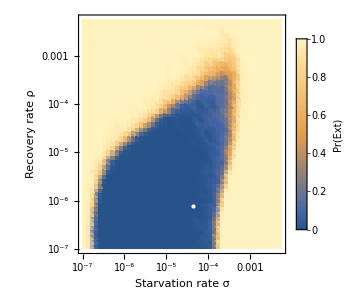

```mathematica
ExtPlot=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[sigvalues]),Log@(Max[sigvalues])},{Log@(Min[sigvalues]),Log@(Max[sigvalues])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}
```

{Log[-(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])],Log[-(1.67857×10^-6)/(M^(1/4) Log[0.292893/(1-0.707107 (1-0.0202 M^0.19)^(1/4))])]}

```mathematica
Starvation
```

0.

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric.pdf"}],ExtPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric.pdf

```mathematica
threshold =(N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality})*0.2/.M->Mass
```

16.6738

```mathematica
Mass
```

10

```mathematica
ts=Table[t,{t,0,100000000,100000}];
```

```mathematica
ts[[5]]
```

400000

```mathematica
ts[[1001]]
```

100000000

```mathematica
4*10^5
```

400000

```mathematica
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]]
```

{4.×10^-6,5.×10^-6,6.25×10^-6,7.8125×10^-6,9.76563×10^-6,0.000012207,0.0000152588,0.0000190735,0.0000238419,0.0000298023,0.0000372529,0.0000465661,0.0000582077,0.0000727596,0.0000909495,0.000113687,0.000142109,0.000177636,0.000222045,0.000277556,0.000346945,0.000433681,0.000542101,0.000677626,0.000847033,0.00105879,0.00132349,0.00165436,0.00206795,0.00258494,0.00323117,0.00403897,0.00504871,0.00631089,0.00788861,0.00986076,0.012326,0.0154074,0.0192593,0.0240741,0.0300927,0.0376158,0.0470198,0.0587747,0.0734684,0.0918355,0.114794,0.143493,0.179366,0.224208}